```mathematica
NGAB[list_, n_] := Module[{currentList = list, nextList, i, points},

(* iterasi sesuai aturan sebanyak n kali untuk memperbarui list*)
Print["Hasil Iterasi:"]
Print[currentList]
For[i = 1, i <= n, i++,
nextList = Mod[{
currentList[[1]]+currentList[[2]],
currentList[[2]]+currentList[[3]],
currentList[[3]]+currentList[[4]],
currentList[[4]]+currentList[[5]],
currentList[[5]]+currentList[[6]],
currentList[[6]]+currentList[[1]]
}, 10];
Print[nextList];
currentList = nextList;
];

(* Membuat tiga titik *)
titik1 = {currentList[[1]],currentList[[2]]};
titik2 = {currentList[[3]],currentList[[4]]};
titik3 = {currentList[[5]],currentList[[6]]};
titikList = {titik1, titik2, titik3};
Print["Titik yang didapatkan adalah ", titik1,", ",titik2,", ", "dan ",titik3, "."];

(* Cek apakah ketiga titik dapat membentuk segitiga *)
(* Digunakan Triangle Inequality *)
AB=Sqrt[(titik2[[1]]-titik1[[1]])^2+(titik2[[2]]-titik1[[2]])^2];
BC=Sqrt[(titik3[[1]]-titik2[[1]])^2+(titik3[[2]]-titik2[[2]])^2];
CA=Sqrt[(titik3[[1]]-titik1[[1]])^2+(titik3[[2]]-titik1[[2]])^2];
isSegitiga = AB+BC>CA&&AB+CA>BC&&BC+CA>AB;

If[isSegitiga, Print["Ketiga titik yang didapatkan bisa membentuk segitiga."];

(* Menghitung sudut-sudut segitiga dengan aturan Cosinus *)
sudutA=N[ArcCos[(BC^2+CA^2-AB^2)/(2*BC*CA)]*180/Pi];
sudutB=N[ArcCos[(AB^2+CA^2-BC^2)/(2*AB*CA)]*180/Pi];
sudutC=N[ArcCos[(AB^2+BC^2-CA^2)/(2*AB*BC)]*180/Pi];
sudutList=Sort[{sudutA, sudutB,sudutC}];
Print["Sudut-sudut dalam derajat dari segitiga tersebut adalah ",sudutList],
Print["Ketiga titik yang didapatkan tidak bisa membentuk segitiga."]];

(* Jika titik-titik membentuk segitiga, maka akan digambar pada bidang Kartesius*)
If[isSegitiga,ListLinePlot[{titik1,titik2,titik3,titik1}]]
]
```

Hasil Iterasi:

{3,1,4,1,5,9}

{4,5,5,6,4,2}

{9,0,1,0,6,6}

{9,1,1,6,2,5}

Titik yang didapatkan adalah {9,1}, {1,6}, dan {2,5}.

Ketiga titik yang didapatkan bisa membentuk segitiga.

Sudut-sudut dalam derajat dari segitiga tersebut adalah {2.2605,12.9946,164.745}

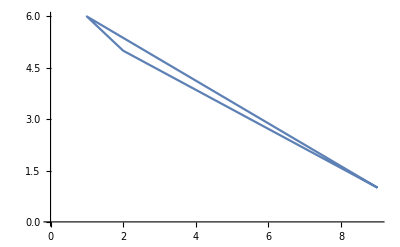

```mathematica
NGAB[{3,1,4,1,5,9}, 3]
```